# Optimal Bandwidth - Parabolic

```mathematica
(* Constants and Unit Conversion*)
```

```mathematica
h2ev=27.211;ev2j=1.602*10^-19;q=1.602*10^-19;mass=9.11*10^-31;bohr2m=5.29*10^-11;
au2sec=2.4188*10^-17;
au2cond=(q/au2sec)^2/bohr2m^3*au2sec^3/mass;
kB=8.6173303*10^-5/h2ev;
T={1,2,3,4,5,6,7,8,9,10}*100;
```

### Average Group Velocity for 3D Parabolic

```mathematica
Clear[kx,m]
energy=1/(2m)(kx^2+ky^2+kz^2);r=Sqrt[2*m*en];
vx2=D[energy,kx]^2;
Print["Velocity squared : ",vx2];
kx=r*Sin[θ]*Cos[ϕ];

norm=Integrate[Integrate[r^2 Sin[θ],{θ,0,π}],{ϕ,0,2π}];
vavg3dpara=Integrate[Integrate[vx2*r^2 Sin[θ],{θ,0,π}],{ϕ,0,2π}]/norm;
Print["Average velocity squared : ",vavg3dpara];
Clear[kx]
```

Velocity squared : kx^2/m^2

Average velocity squared : (2 en)/(3 m)

### Average Group Velocity for 2D Parabolic

```mathematica
Clear[kx,m]
energy=1/(2m)(kx^2+ky^2);r=Sqrt[2*m*en];
vx2=D[energy,kx]^2;
Print["Velocity squared : ",vx2];
kx=r*Cos[θ];

norm=Integrate[r,{θ,0,2π}];
vavg2dpara=Integrate[vx2*r,{θ,0,2π}]/norm;
Print["Average velocity squared : ",vavg2dpara];
Clear[kx]
```

Velocity squared : kx^2/m^2

Average velocity squared : en/m

### Find Optimal Bandwidth

```mathematica
m=0.067;
v2=vavg3dpara;
bz=(1/15.)*2π/2;Vbz=bz^-3*(2π/2)^3/8;
vs=4000/(bohr2m/au2sec);ρ=5000/(mass/bohr2m^3);Δ=0.4;
normalizer=1691.72; (* For confining the band in the BZ *)
tauprefactor=(vs^2*ρ*normalizer)/(π*kB*temp*Δ^2);
(*Ef=Range[-0.2,0.2,0.01]/h2ev;Nef=Length[Ef];*)
Ef=Range[-0.22,0.2,0.002]/h2ev;
Nef=Length[Ef];
T={2,3,5,7,10}*100;
NT=Length[T];
f=1/(Exp[(en-ef)/(kB*temp)]+1);df=-D[f,en];

σ=tauprefactor/Vbz*Integrate[v2*df,{en,0,x},GenerateConditions->False];
ζ=tauprefactor/(Vbz*temp)*Integrate[v2*(ef-en)*df,{en,0,x},GenerateConditions->False];
κ=tauprefactor/(Vbz*temp)*Integrate[v2*(ef-en)^2*df,{en,0,x},GenerateConditions->False]-ζ^2/σ temp;
zT=ζ^2/(σ*(κ+κlat))temp/.ef->Ef/.temp->T;
α=ζ/σ/.ef->Ef/.temp->T;
PF=ζ^2/σ/.ef->Ef/.temp->T;
L=κ/(σ*temp)/.ef->Ef/.temp->T;
```

```mathematica
(*LogLogPlot[σ*au2cond,{x,10^-5,10^-1},Frame->True,PlotRange->{Automatic,{10^0,10^6}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-15,15}],None},{Table[{10^i,Superscript[10,i]},{i,-15,15}],None}},ImageSize->500]*)
(*
LogPlot[κ*h2ev*ev2j/bohr2m/au2sec,{x,0,1.5/h2ev}]
Plot[α*h2ev*ev2j/q*10^6,{x,0,1.5/h2ev},PlotRange->Full]
LogPlot[L*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8,{x,0,1.5/h2ev}]*)
```

```mathematica
ztvswidth1={};ztvswidth2={};ztvswidth3={};ztvswidth4={};ztvswidth5={};ztvswidth6={};ztvswidth7={};ztvswidth8={};
ztvswidth9={};
ztvswidth10={};

t=T/100;
klat=Reverse@{25,15,10,7,4.5,3,2,1.2,0.8,0.5,0.3,0.2}/(h2ev*ev2j/bohr2m/au2sec);

Do[
max={};maxen={};
Do[
myzt=zT⟦ef,1⟧/.κlat->klat⟦i⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth1,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,2⟧/.κlat->klat⟦i⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth2,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,3⟧/.κlat->klat⟦i⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth3,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,4⟧/.κlat->klat⟦i⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth4,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,5⟧/.κlat->klat⟦i⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth5,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

,{i,Length[klat]}];

Do[
max={};maxen={};
Do[
myzt=zT⟦ef,i⟧/.κlat->klat⟦1⟧;
myseebeck=α⟦ef,i⟧/.κlat->klat⟦1⟧;
result=Maximize[{myzt,x>0},x,myseebeck<0];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth6,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,i⟧/.κlat->klat⟦4⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth7,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,i⟧/.κlat->klat⟦7⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth8,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,i⟧/.κlat->klat⟦10⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth9,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,i⟧/.κlat->klat⟦12⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth10,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

Print[i]

,{i,NT}]//AbsoluteTiming
```

```mathematica
hizt={};
Do[
max={};maxen={};
Do[
myzt=zT⟦ef,i⟧/.κlat->klat⟦1⟧;
myseebeck=α⟦ef,i⟧/.κlat->klat⟦1⟧;
result=Maximize[{myzt,x>0},x(*,myseebeck<0*)];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[hizt,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];
,{i,NT}]//AbsoluteTiming
hizt[[1]]
```

$Aborted

{0.141489,0.2,14.0325}

```mathematica
ζ/.{temp->200,ef->ztvswidth1⟦All,2⟧,x->ztvswidth1⟦All,1⟧}
σ/.{temp->200,ef->ztvswidth1⟦All,2⟧,x->ztvswidth1⟦All,1⟧}
h2ev*ev2j/q*10^6*(ζ/σ)/.{temp->200,ef->ztvswidth1⟦All,2⟧,x->ztvswidth1⟦All,1⟧}
(ζ^2/(σ*(κ+κlat))temp)/.{temp->200,ef->ztvswidth1⟦All,2⟧,κlat->0.2/(h2ev*ev2j/bohr2m/au2sec),x->ztvswidth1⟦All,1⟧}
```

{-5.16525×10^-42,-4.77375×10^-39,-1.89629×10^-35,-2.68912×10^-32,-1.00925×10^-29,-1.05711×10^-26,-1.6477×10^-24,-1.59815×10^-22,-1.28497×10^-20,-2.72612×10^-19,3.63075×10^-18,1.34×10^-17}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.38472×10^-14}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,4348.72}

```mathematica
ztvswidth1⟦All,{1,3}⟧
ztvswidth6⟦All,{1,3}⟧
```

{{0.141489,14.0325},{0.145814,11.6415},{0.151063,9.04424},{0.15566,7.03418},{0.159414,5.57092},{0.163818,4.05548},{0.167016,3.08954},{0.169914,2.31078},{0.172692,1.64896},{0.174627,1.2366},{0.176483,0.877915},{0.178314,0.558639}}

{{0.141489,14.0325},{0.123121,14.1009},{0.107557,13.0271},{0.163777,13.3599},{0.215425,16.2472}}

```mathematica
Length[T]
```

5

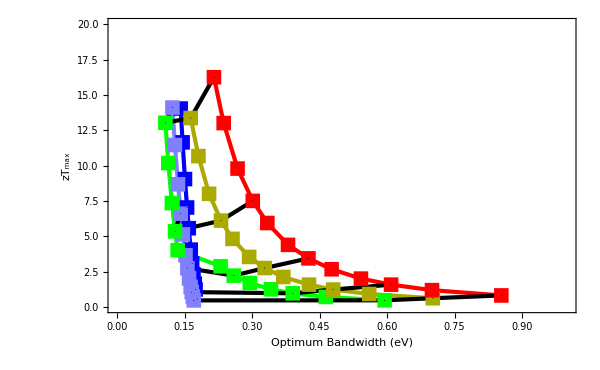

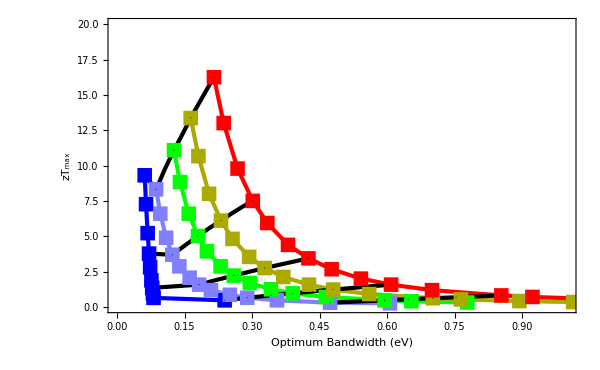

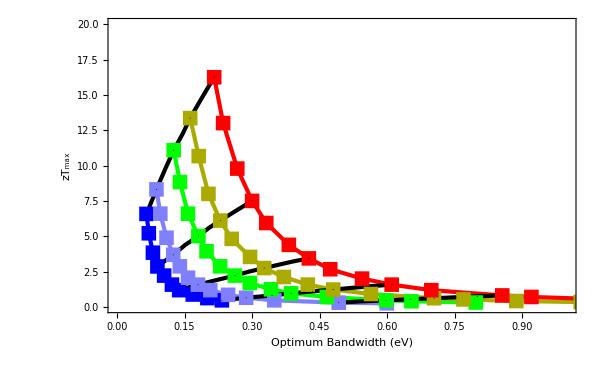

```mathematica
ListPlot[{ztvswidth1⟦Range[10],{1,3}⟧,ztvswidth2⟦Range[12],{1,3}⟧,ztvswidth3⟦Range[12],{1,3}⟧,ztvswidth4⟦All,{1,3}⟧,ztvswidth5⟦All,{1,3}⟧,ztvswidth6⟦Range[5],{1,3}⟧,ztvswidth7⟦Range[5],{1,3}⟧,ztvswidth8⟦Range[5],{1,3}⟧,ztvswidth9⟦Range[5],{1,3}⟧,ztvswidth10⟦Range[5],{1,3}⟧},Frame->True,Joined->True,FrameLabel->{"Optimum Bandwidth (eV)","zT_max"},FrameStyle->Directive[Black,Thick,25],ImageSize->600,PlotStyle->{{Blue,Thickness[0.005]},{Lighter[Blue,0.5],Thickness[0.005]},{Green,Thickness[0.005]},{Darker[Yellow],Thickness[0.005]},{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]}},PlotMarkers->{{■,15},{■,15},{■,15},{■,15},{■,15},{●,1},{●,1},{●,1},{●,1},{●,1}},PlotRange->{{0,1},{0,20}}]
```

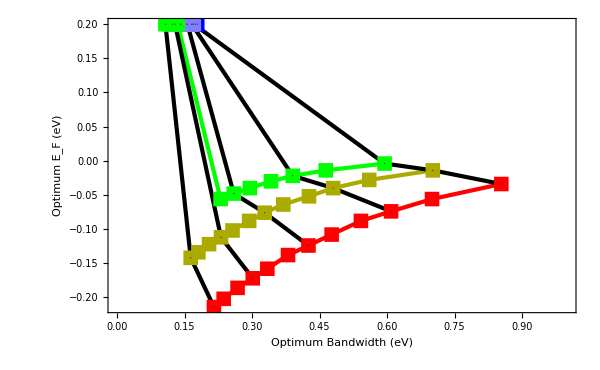

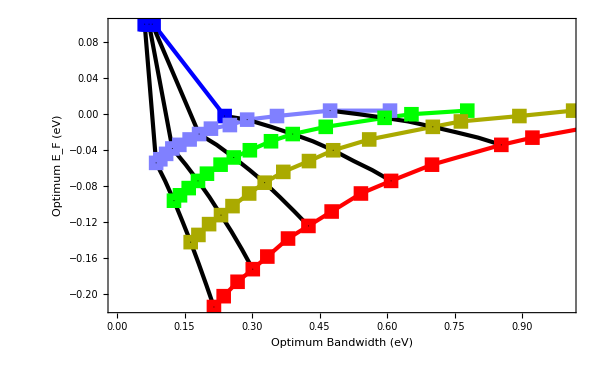

```mathematica
ListPlot[{ztvswidth1⟦Range[12],{1,2}⟧,ztvswidth2⟦Range[12],{1,2}⟧,ztvswidth3⟦Range[12],{1,2}⟧,ztvswidth4⟦All,{1,2}⟧,ztvswidth5⟦All,{1,2}⟧,ztvswidth6⟦Range[5],{1,2}⟧,ztvswidth7⟦Range[5],{1,2}⟧,ztvswidth8⟦Range[5],{1,2}⟧,ztvswidth9⟦Range[5],{1,2}⟧,ztvswidth10⟦Range[5],{1,2}⟧},Frame->True,Joined->True,FrameLabel->{"Optimum Bandwidth (eV)","Optimum E_F (eV)"},FrameStyle->Directive[Black,Thick,25],ImageSize->600,PlotStyle->{{Blue,Thickness[0.005]},{Lighter[Blue,0.5],Thickness[0.005]},{Green,Thickness[0.005]},{Darker[Yellow],Thickness[0.005]},{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]}},PlotMarkers->{{■,15},{■,15},{■,15},{■,15},{■,15},{●,1},{●,1},{●,1},{●,1},{●,1}},PlotRange->{{0,1},Automatic}]
```

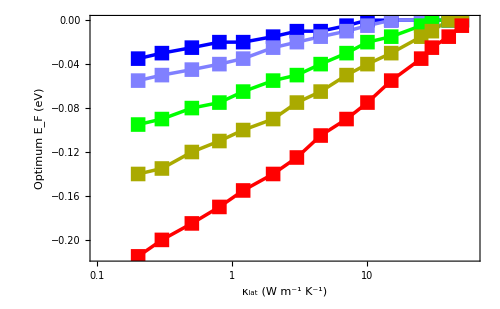

```mathematica
ListLogLinearPlot[{Transpose[{klat*(h2ev*ev2j/bohr2m/au2sec),ztvswidth1⟦All,2⟧}],Transpose[{klat*(h2ev*ev2j/bohr2m/au2sec),ztvswidth2⟦All,2⟧}],
Transpose[{klat*(h2ev*ev2j/bohr2m/au2sec),ztvswidth3⟦All,2⟧}],
Transpose[{klat*(h2ev*ev2j/bohr2m/au2sec),ztvswidth4⟦All,2⟧}],Transpose[{klat*(h2ev*ev2j/bohr2m/au2sec),ztvswidth5⟦All,2⟧}]},Frame->True,FrameStyle->Directive[Black,Thick,20],FrameLabel->{"κ_lat (W m^-1 K^-1)","Optimum E_F (eV)"},PlotStyle->{{Blue,Thickness[0.005]},{Lighter[Blue,0.5],Thickness[0.005]},{Green,Thickness[0.005]},{Darker[Yellow],Thickness[0.005]},{Red,Thickness[0.005]}},PlotMarkers->{{■,15},{■,15},{■,15},{■,15},{■,15}},PlotRange->{{0.1,60},Automatic},Joined->True,ImageSize->500]
```

### Old

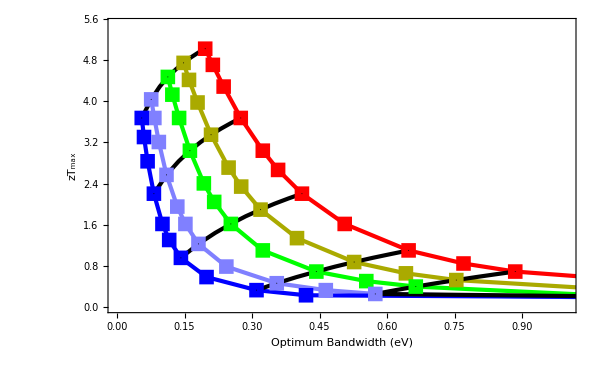

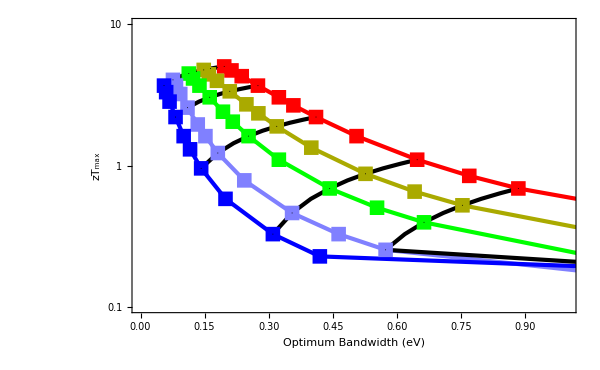

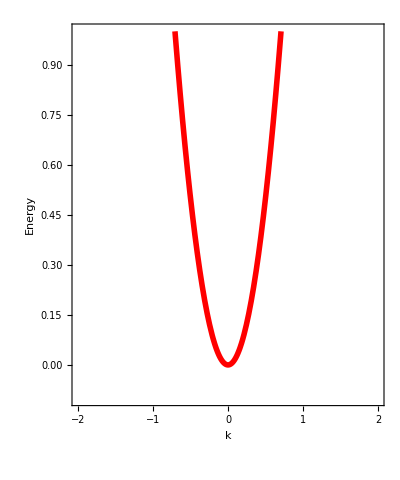

```mathematica
Show[
Plot[2*k^2,{k,-0.8,0.8},PlotRange->{{-2,2},{-0.1,1}},Frame->True,FrameLabel->{"k","Energy"},FrameTicks->{{None,None},{None,None}},FrameStyle->Directive[Black,Thick,25],ImageSize->400,AspectRatio->1.2,PlotStyle->{Red,Thickness[0.01]}](*,
Plot[{k^2/100,k^2/100+0.8},{k,-10.8,10.8},PlotRange->{{-2,2},{-0.2,1.5}},Frame->True,FrameLabel->{"k","Energy"},FrameTicks->{{None,None},{None,None}},FrameStyle->Directive[Black,Thick,25],ImageSize->400,AspectRatio->1.2,PlotStyle->{{Blue,Thickness[0.01]},{Blue,Thickness[0.01]}}]*)
]
```

```mathematica
(klat*h2ev*ev2j/bohr2m/au2sec)
```

{80.,40.,30.,20.,10.,5.,3.,2.,1.,0.5,0.3,0.2}

```mathematica
klat
```

{2.34822×10^-8,1.17411×10^-8,8.80582×10^-9,5.87055×10^-9,2.93527×10^-9,1.46764×10^-9,8.80582×10^-10,5.87055×10^-10,2.93527×10^-10,1.46764×10^-10,8.80582×10^-11,5.87055×10^-11}

```mathematica
Length[klat]
```

12

# Optimal Bandwidth - Quartic

```mathematica
h2ev=27.211;ev2j=1.602*10^-19;q=1.602*10^-19;mass=9.11*10^-31;bohr2m=5.29*10^-11;
au2sec=2.4188*10^-17;
au2cond=(q/au2sec)^2/bohr2m^3*au2sec^3/mass;
kB=8.6173303*10^-5/h2ev;
T={1,2,3,4,5,6,7,8,9,10}*100;
```

### Average Group Velocity for 3D Quartic

```mathematica
Clear[kx,ky,kz,c,m]
energy=c(kx^2+ky^2+kz^2)^2;r=(en/c)^(1/4);
vx2=D[energy,kx]^2;
Print["Velocity squared : ",vx2];
kx=r*Sin[θ]*Cos[ϕ];
ky=r*Sin[θ]*Sin[ϕ];
kz=r*Cos[θ];

norm=Integrate[Integrate[r^2 Sin[θ],{θ,0,π}],{ϕ,0,2π}];
vavg3dquartic=Integrate[Integrate[vx2*r^2 Sin[θ],{θ,0,π}],{ϕ,0,2π}]/norm;
Print["Average velocity squared : ",vavg3dquartic];
Clear[kx,ky,kz]
```

Velocity squared : 16 c^2 kx^2 (kx^2+ky^2+kz^2)^2

Average velocity squared : (16 en^2)/(3 √(en/c))

```mathematica
c=1/(2*0.067)/inflect^2;
vel=(D[energy,kx])^2;
vellist=ConstantArray[0,Nk];elist=ConstantArray[0,Nk];
Do[
elist⟦i⟧=energy/.{kx->klist⟦1,i⟧,ky->klist⟦2,i⟧,kz->klist⟦3,i⟧};
vellist⟦i⟧=vel/.{kx->klist⟦1,i⟧,ky->klist⟦2,i⟧,kz->klist⟦3,i⟧};
,{i,Nk}]
```

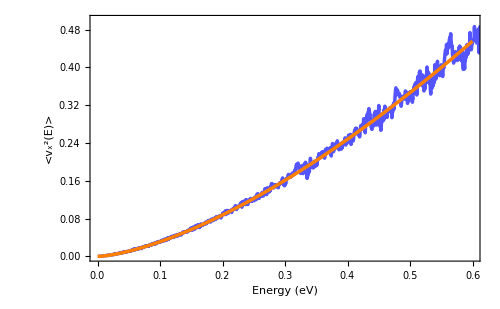

```mathematica
weight=(*wk*10^5*)1;r=Nk;

move=50;
order=Ordering[elist];
Show[ListPlot[Transpose[{MovingMap[Mean,Sort[elist]*h2ev,move],MovingMap[Mean,weight*vellist⟦order⟧,move]}],PlotRange->{{0,0.6},{0,0.5}},PlotStyle->{Lighter[Blue],Thickness[0.005]},Frame->True,FrameLabel->{"Energy (eV)","<v_x^2(E)>"},Joined->True,FrameStyle->Directive[Black,25,Thick],Frame->True,ImageSize->500],
Plot[vavg3dquartic/.en->(enn/h2ev),{enn,0,0.6},PlotStyle->{Orange,Thickness[0.005]},Frame->True,FrameLabel->{"Energy (eV)","<v_x^2(E)>"},FrameStyle->Directive[Black,25,Thick],Frame->True,ImageSize->500]
]
```

```mathematica
vavg3dquartic
vavg3dpara
ζ^2/(σ*(κ+κlat))temp
```

139.129 en^(3/2)

(2 en)/(3 m)

(6846.58 Integrate[(4.39329×10^7 ⅇ^((315771. (-ef+en))/temp) (ef-en) en^(3/2))/((1+ⅇ^((315771. (-ef+en))/temp))^2 temp),{en,0,x},GenerateConditions→False]^2)/(temp^2 Integrate[(4.39329×10^7 ⅇ^((315771. (-ef+en))/temp) en^(3/2))/((1+ⅇ^((315771. (-ef+en))/temp))^2 temp),{en,0,x},GenerateConditions→False] (κlat-(6846.58 Integrate[(4.39329×10^7 ⅇ^((315771. (-ef+en))/temp) (ef-en) en^(3/2))/((1+ⅇ^((315771. (-ef+en))/temp))^2 temp),{en,0,x},GenerateConditions→False]^2)/(temp^2 Integrate[(4.39329×10^7 ⅇ^((315771. (-ef+en))/temp) en^(3/2))/((1+ⅇ^((315771. (-ef+en))/temp))^2 temp),{en,0,x},GenerateConditions→False])+1/temp^2 6846.58 Integrate[(4.39329×10^7 ⅇ^((315771. (-ef+en))/temp) (ef-en)^2 en^(3/2))/((1+ⅇ^((315771. (-ef+en))/temp))^2 temp),{en,0,x},GenerateConditions→False]))

### Find Optimal Bandwidth

```mathematica
bz=(1/15.)*2π/2;Vbz=bz^-3*(2π/2)^3/8;inflect=bz/2; (* Define BZ *)
c=1/(2*0.067)/inflect^2; (* Dispersion coefficient *)
v2=vavg3dquartic (* Average velocity in one direction *);
normalizer=1691.72; (* For confining the band in the BZ *)
vs=4000/(bohr2m/au2sec);ρ=5000/(mass/bohr2m^3);
Δ=0.4; (* Parameters for DPS *)
tauprefactor=(vs^2*ρ*normalizer)/(π*kB*temp*Δ^2);

Ef=Range[-0.22,0,0.002]/h2ev;
Nef=Length[Ef];
T={2,3,5,7,10}*100;
NT=Length[T];
f=1/(Exp[(en-ef)/(kB*temp)]+1);df=-D[f,en];

σ=tauprefactor/Vbz*Integrate[v2*df,{en,0,x},GenerateConditions->False];
ζ=tauprefactor/(Vbz*temp)*Integrate[v2*(ef-en)*df,{en,0,x},GenerateConditions->False];
κ=tauprefactor/(Vbz*temp)*Integrate[v2*(ef-en)^2*df,{en,0,x},GenerateConditions->False]-ζ^2/σ temp;
zT=ζ^2/(σ*(κ+κlat))temp/.ef->Ef/.temp->T;
```

$Aborted

```mathematica
α=ζ/σ/.ef->Ef/.temp->T;
PF=ζ^2/σ/.ef->Ef/.temp->T;
L=κ/(σ*temp)/.ef->Ef/.temp->T;
```

```mathematica
LogLogPlot[σ⟦1⟧*au2cond,{x,10^-5,10^-1},Frame->True,PlotRange->{Automatic,{10^0,10^6}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-15,15}],None},{Table[{10^i,Superscript[10,i]},{i,-15,15}],None}},ImageSize->500]
(*
LogPlot[κ*h2ev*ev2j/bohr2m/au2sec,{x,0,1.5/h2ev}]
Plot[α*h2ev*ev2j/q*10^6,{x,0,1.5/h2ev},PlotRange->Full]
LogPlot[L*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8,{x,0,1.5/h2ev}]*)
```

```mathematica
ztvswidth1={};ztvswidth2={};ztvswidth3={};ztvswidth4={};ztvswidth5={};ztvswidth6={};ztvswidth7={};ztvswidth8={};
ztvswidth9={};
ztvswidth10={};

klat=Reverse@{25,15,10,7,4.5,3,2,1.2,0.8,0.5,0.3,0.2}/(h2ev*ev2j/bohr2m/au2sec);

Do[
max={};maxen={};
Do[
myzt=zT⟦ef,2⟧/.κlat->klat⟦i⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth1,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];
Print["HI"];
max={};maxen={};
Do[
myzt=zT⟦ef,3⟧/.κlat->klat⟦i⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth2,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,5⟧/.κlat->klat⟦i⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth3,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,7⟧/.κlat->klat⟦i⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth4,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,10⟧/.κlat->klat⟦i⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth5,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

,{i,Length[klat]}];

Do[
max={};maxen={};
Do[
myzt=zT⟦ef,i⟧/.κlat->klat⟦1⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth6,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,i⟧/.κlat->klat⟦4⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth7,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,i⟧/.κlat->klat⟦7⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth8,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,i⟧/.κlat->klat⟦10⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth9,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

max={};maxen={};
Do[
myzt=zT⟦ef,i⟧/.κlat->klat⟦12⟧;
result=Maximize[{myzt,x>0},x];
AppendTo[max,result⟦1⟧];
AppendTo[maxen,Values[result⟦2⟧]⟦1⟧];
,{ef,Nef}];
maxef=Position[max,Max[max]]⟦1,1⟧;
AppendTo[ztvswidth10,{maxen⟦maxef⟧*h2ev,Ef⟦maxef⟧*h2ev,Max[max]}];

,{i,NT}]
```

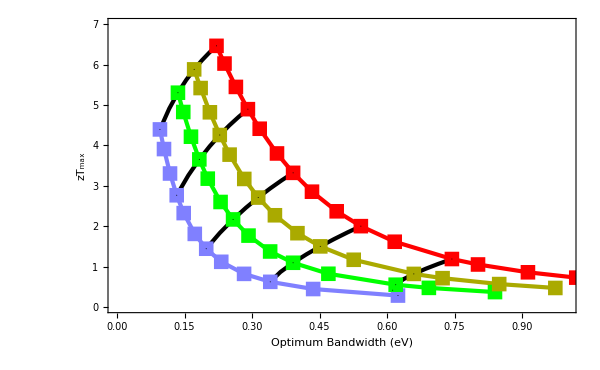

```mathematica
ListPlot[{(*ztvswidth1⟦Range[10]⟧,*)ztvswidth2⟦Range[12]⟧,ztvswidth3⟦Range[14]⟧,ztvswidth4,ztvswidth5,ztvswidth6⟦Range[3,10]⟧,ztvswidth7⟦Range[3,10]⟧,ztvswidth8⟦Range[3,10]⟧,ztvswidth9⟦Range[3,10]⟧,ztvswidth10⟦Range[3,10]⟧},Frame->True,Joined->True,FrameLabel->{"Optimum Bandwidth (eV)","zT_max"},FrameStyle->Directive[Black,Thick,25],ImageSize->600,PlotStyle->{(*{Blue,Thickness[0.005]},*){Lighter[Blue,0.5],Thickness[0.005]},{Green,Thickness[0.005]},{Darker[Yellow],Thickness[0.005]},{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]}},PlotMarkers->{(*{■,15},*){■,15},{■,15},{■,15},{■,15},{●,1},{●,1},{●,1},{●,1},{●,1}},PlotRange->{{0,1},{0,7}}]
```

```mathematica
(Log[ztvswidth2⟦12,2⟧]-Log[ztvswidth2⟦1,2⟧])/(Log[ztvswidth2⟦12,1⟧]-Log[ztvswidth2⟦1,1⟧])
(Log[ztvswidth2⟦12,2⟧]-Log[ztvswidth2⟦1,2⟧])/(Log[klat⟦12⟧]-Log[klat⟦1⟧])
```

-1.46015

-0.568044

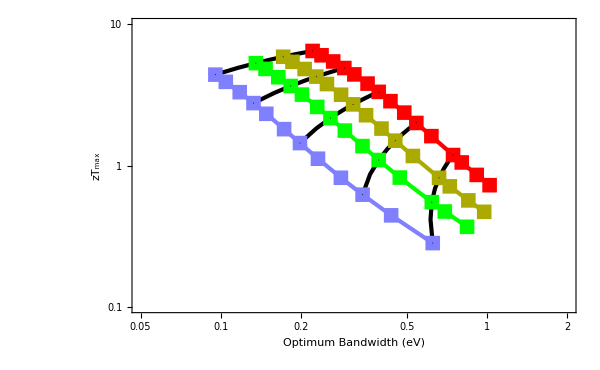

```mathematica
ListLogLogPlot[{(*ztvswidth1⟦Range[10]⟧,*)ztvswidth2⟦Range[12]⟧,ztvswidth3⟦Range[14]⟧,ztvswidth4,ztvswidth5,ztvswidth6⟦Range[3,10]⟧,ztvswidth7⟦Range[3,10]⟧,ztvswidth8⟦Range[3,10]⟧,ztvswidth9⟦Range[3,10]⟧,ztvswidth10⟦Range[3,10]⟧},Frame->True,Joined->True,FrameLabel->{"Optimum Bandwidth (eV)","zT_max"},FrameStyle->Directive[Black,Thick,25],ImageSize->600,PlotStyle->{(*{Blue,Thickness[0.005]},*){Lighter[Blue,0.5],Thickness[0.005]},{Green,Thickness[0.005]},{Darker[Yellow],Thickness[0.005]},{Red,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]}},PlotMarkers->{(*{■,15},*){■,15},{■,15},{■,15},{■,15},{●,1},{●,1},{●,1},{●,1},{●,1}},PlotRange->{{0.05,2},{0.1,10}}]
```

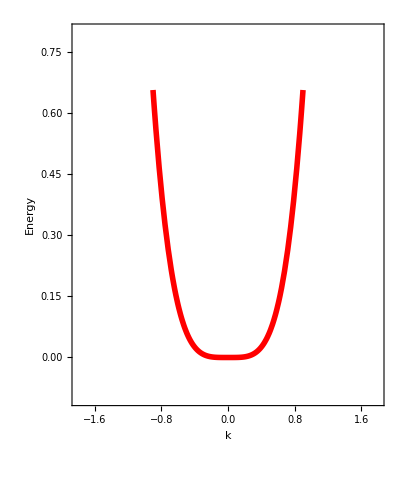

```mathematica
Plot[k^4,{k,-0.9,0.9},PlotRange->{{-1.8,1.8},{-0.1,0.8}},Frame->True,FrameLabel->{"k","Energy"},FrameTicks->{{None,None},{None,None}},FrameStyle->Directive[Black,Thick,25],ImageSize->400,AspectRatio->1.2,PlotStyle->{Red,Thickness[0.01]}]
```

### Quartic DOS

```mathematica
broad=10^-2;
G4d=1/(en-elist*h2ev+I*broad);

dos4d=-Im[Total[G4d*wk]];
enmax1=h2ev*energy/.{kx->inflect,ky->inflect,kz->inflect};
enmax2=h2ev*1/(2*0.067)(kx^2+ky^2+kz^2)/.{kx->inflect,ky->inflect,kz->inflect};
dos4d=dos4d/NIntegrate[dos4d,{en,0,enmax1}]/2;
dospara=(Sqrt[2] 0.067^(3/2))/π^2 Sqrt[en/h2ev];
dospara=dospara*NIntegrate[dos4d,{en,0,enmax1}]/NIntegrate[dospara,{en,0,enmax2}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {14.992}. NIntegrate obtained 1.0633 and 0.00283582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in en near {en} = {14.992}. NIntegrate obtained 0.5 and 0.0013335 for the integral and error estimates.

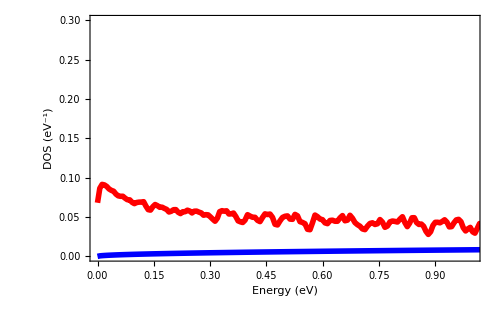

```mathematica
dosplot=Plot[{dos4d,dospara},{en,0,enmax},Exclusions->None,PlotStyle->{{Thickness[0.008],Red},{Thickness[0.008],Blue},{Thickness[0.008],Black}},PlotRange->{{0,1},{0,0.3}},Frame->True,FrameStyle->Directive[Black,25,Thick],FrameLabel->{"Energy (eV)","DOS (eV^-1)"},ImageSize->500]
```

```mathematica
Integrate[Integrate[Integrate[rr*Sin[ϕ],{ϕ,0,π}],{θ,0,2π}],{rr,0,r}]
Integrate[Integrate[Integrate[rr^2*Sin[ϕ],{ϕ,0,π}],{θ,0,2π}],{rr,0,r}]
Integrate[Integrate[Integrate[rr^3*Sin[ϕ],{ϕ,0,π}],{θ,0,2π}],{rr,0,r}]
```

(4 π r^3)/3

π r^4

```mathematica
FullSimplify[(3(4/3 π))/(2(1/(2m))^(3/2))*Sqrt[en]]
FullSimplify[2π*Sqrt[en/(1/(2m))^3]]
FullSimplify[2π*Sqrt[en/(1/(2m))^3]/(4/3 π)]
```

(4 √2 √en π)/(1/m)^(3/2)

4 √2 √(en m^3) π

3 √2 √(en m^3)

```mathematica
dospara
2π*Sqrt[(en/h2ev)/(1/(2*0.067))^3]
```

0.0434344 √en

0.0590833 √en

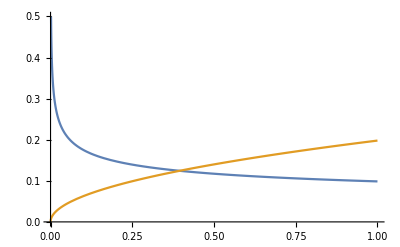

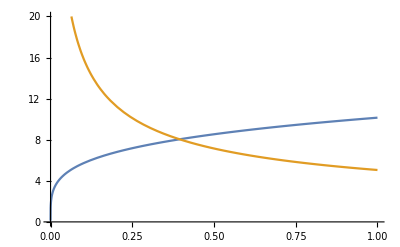

```mathematica
dospara=2π*Sqrt[(en/h2ev)/(1/(2*0.15))^3];
c=1/(2*0.15)/inflect^2;
dosquart=(3*(4/3 π))/4 c^(-3/4)(en/h2ev)^(-1/4);
Plot[{dosquart,dospara},{en,0,1},PlotRange->{Automatic,{0,0.5}}]
Plot[{1/dosquart,1/dospara},{en,0,1},PlotRange->{Automatic,{0,20}}]
```